```mathematica
ABMInputs200=Import["/Users/thorsilver/Documents/ABM-for-social-care/LPtau200runs_GEMSA_inputs.csv"];

ABMOutputs200=Import["/Users/thorsilver/Documents/ABM-for-social-care/LPtau200runs GEMSA outputs only.csv"];
```

```mathematica
ABMOutputs200=Function[x,x/1000]/@ABMOutputs200; 
ABMAssoc200 = AssociationThread[ABMInputs200 -> Flatten[ABMOutputs200]];
ABMnewData200=Dataset[ABMAssoc200];
ABMNormal200=Normal[ABMAssoc200];
ABMNormalRandom=RandomSample[ABMNormal200];
ABMtrain200=TakeDrop[ABMNormal200,160];
ABMtest200=ABMtrain200[[2]];
ABMtraining200=ABMtrain200[[1]];
trainDevSplit200=TakeDrop[ABMtraining200,128];
finalTrain200=trainDevSplit200[[1]];
finalDev200=trainDevSplit200[[2]];
finaltest200=ABMtest200;
```

```mathematica
Length[finalDev200]
Length[finalTrain200]
Length[finaltest200]
```

32

128

40

```mathematica
pRFv200=Predict[finalTrain200,Method->"RandomForest"]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

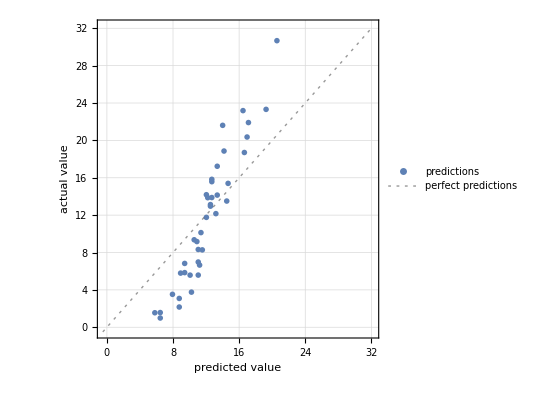

16.9357

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 5.66 ± 0.35
Method | RandomForest
Single evaluation time | 3.55 ms/example
Batch evaluation speed | 44.2 examples/ms
Loss | 3.19 ± 0.061
Model memory | 235. kB
Training examples used | 128 examples
Training time | 2.14 s
 |

```mathematica
pmRFv200=PredictorMeasurements[pRFv200,finaltest200]
pmRFv200["ComparisonPlot"]
pmRFv200["MeanSquare"]
Information[pRFv200]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

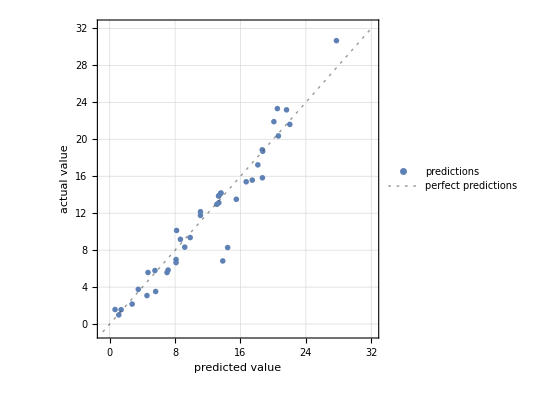

3.77753

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 3.71 ± 1.1
Method | GradientBoostedTrees
Single evaluation time | 3.78 ms/example
Batch evaluation speed | 43.4 examples/ms
Loss | 64.2 ± 29.
Model memory | 389. kB
Training examples used | 128 examples
Training time | 1.4 s
 |

```mathematica
pXGTv200=Predict[finalTrain200,Method->"GradientBoostedTrees"]
pmXGTv200=PredictorMeasurements[pXGTv200,finaltest200]
pmXGTv200["ComparisonPlot"]
pmXGTv200["MeanSquare"]
Information[pXGTv200]
```

```mathematica
pNNv200= Predict[finalTrain200,Method->{"NeuralNetwork", "NetworkDepth"->3,"NetworkType"->"FullyConnected", "L2Regularization"->0.05, MaxTrainingRounds->16000}]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

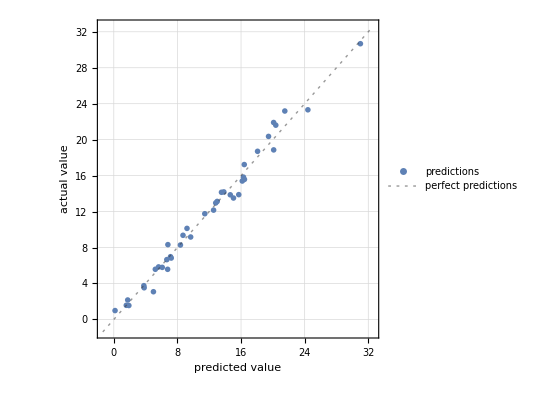

0.785093

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 2.8 ± 1.5
Method | NeuralNetwork
Single evaluation time | 2.34 ms/example
Batch evaluation speed | 49.7 examples/ms
Loss | 2.3 ± 0.52
Model memory | 253. kB
Training examples used | 128 examples
Training time | 1 33
 |

```mathematica
pmNNv200=PredictorMeasurements[pNNv200,finaltest200]
pmNNv200["ComparisonPlot"]
pmNNv200["MeanSquare"]
Information[pNNv200]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

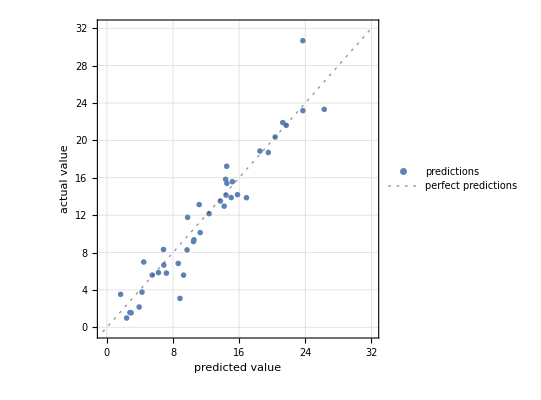

4.28377

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 3.66 ± 0.54
Method | GaussianProcess
Single evaluation time | 3.59 ms/example
Batch evaluation speed | 30.9 examples/ms
Loss | 2.63 ± 0.083
Model memory | 265. kB
Training examples used | 128 examples
Training time | 2.02 s
 |

```mathematica
pGPEv200=Predict[finalTrain200,Method->"GaussianProcess"]
pmGPEv200=PredictorMeasurements[pGPEv200,finaltest200]
pmGPEv200["ComparisonPlot"]
pmGPEv200["MeanSquare"]
Information[pGPEv200]
```

```mathematica
pNNv200l3= Predict[finalTrain200,Method->{"NeuralNetwork", "NetworkDepth"->3,"NetworkType"->"FullyConnected", "L2Regularization"->0.05, MaxTrainingRounds->24000}]
pmNNv200l3=PredictorMeasurements[pNNv200l3,finaltest200]
pmNNv200l3["ComparisonPlot"]
pmNNv200l3["MeanSquare"]
Information[pNNv200l3]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

-Graphics-

0.785093

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 2.8 ± 1.5
Method | NeuralNetwork
Single evaluation time | 2.19 ms/example
Batch evaluation speed | 44.8 examples/ms
Loss | 2.3 ± 0.52
Model memory | 253. kB
Training examples used | 128 examples
Training time | 2 13
 |

PredictorFunction[…]

PredictorMeasurementsObject[…]

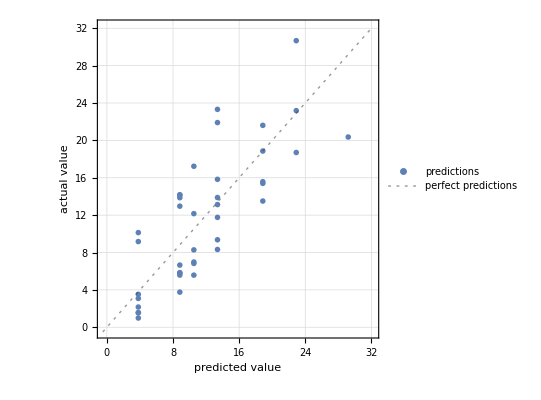

19.7339

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 5.67 ± 0.6
Method | DecisionTree
Single evaluation time | 1.31 ms/example
Batch evaluation speed | 378. examples/ms
Loss | 3.29 ± 0.19
Model memory | 143. kB
Training examples used | 128 examples
Training time | 332. ms
 |

```mathematica
pDTv200=Predict[finalTrain200,Method->"DecisionTree"]
pmDTv200=PredictorMeasurements[pDTv200,finaltest200]
pmDTv200["ComparisonPlot"]
pmDTv200["MeanSquare"]
Information[pDTv200]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

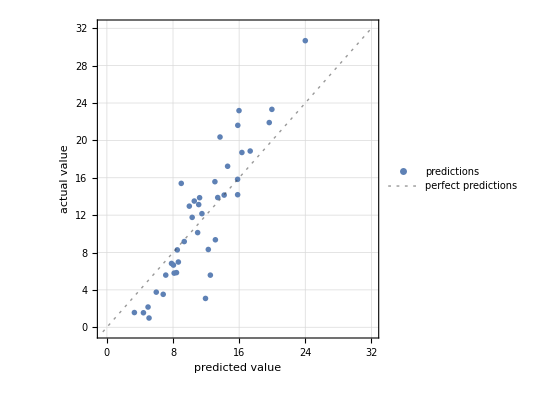

12.8954

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 5.58 ± 0.66
Method | NearestNeighbors
Single evaluation time | 1.37 ms/example
Batch evaluation speed | 89.2 examples/ms
Loss | 3.21 ± 0.13
Model memory | 155. kB
Training examples used | 128 examples
Training time | 333. ms
 |

```mathematica
pNearestv200=Predict[finalTrain200,Method->"NearestNeighbors"]
pmNearestv200=PredictorMeasurements[pNearestv200,finaltest200]
pmNearestv200["ComparisonPlot"]
pmNearestv200["MeanSquare"]
Information[pNearestv200]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

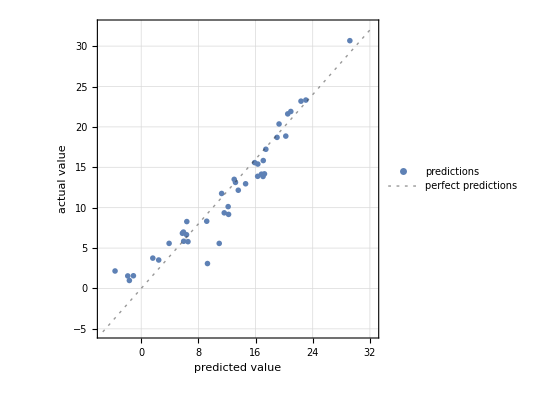

5.23679

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 3.59 ± 0.46
Method | LinearRegression
Single evaluation time | 1.53 ms/example
Batch evaluation speed | 289. examples/ms
Loss | 2.58 ± 0.086
Model memory | 257. kB
Training examples used | 128 examples
Training time | 1.47 s
 |

```mathematica
pLRv200=Predict[finalTrain200,Method->"LinearRegression"]
pmLRv200=PredictorMeasurements[pLRv200,finaltest200]
pmLRv200["ComparisonPlot"]
pmLRv200["MeanSquare"]
Information[pLRv200]
```

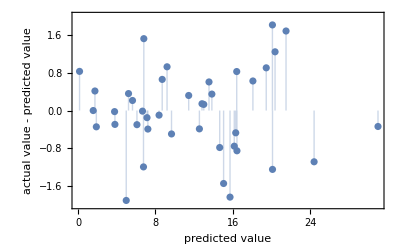

```mathematica
pmNNv200["ResidualPlot"]
```

```mathematica
pmNNv200l3["ResidualPlot"]
```

-Graphics-

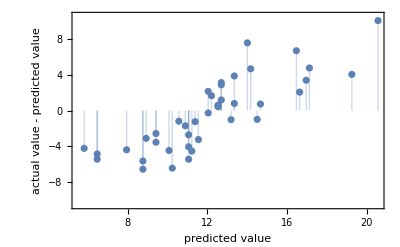

```mathematica
pmRFv200["ResidualPlot"]
```

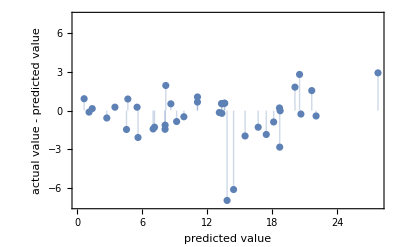

```mathematica
pmXGTv200["ResidualPlot"]
```

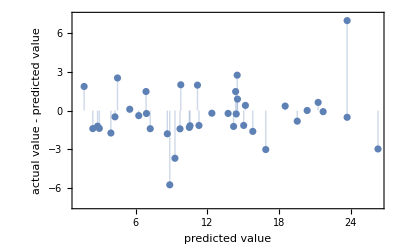

```mathematica
pmGPEv200["ResidualPlot"]
```

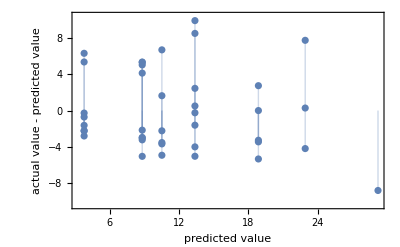

```mathematica
pmDTv200["ResidualPlot"]
```

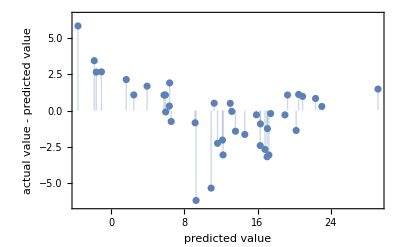

```mathematica
pmLRv200["ResidualPlot"]
```

### MeanSquare

```mathematica
pmNNv200["MeanSquare"]
pmDTv200["MeanSquare"]
pmLRv200["MeanSquare"]
pmRFv200["MeanSquare"]
pmXGTv200["MeanSquare"]
pmGPEv200["MeanSquare"]
pmLRv200["MeanSquare"]
pmNearestv200["MeanSquare"]
```

0.785093

19.7339

5.23679

16.9357

3.77753

4.28377

5.23679

12.8954

PredictorFunction[…]

PredictorMeasurementsObject[…]

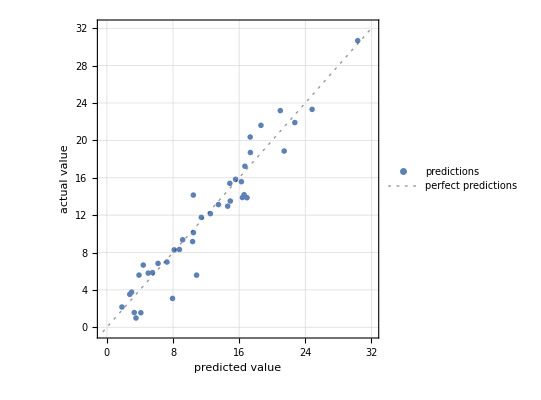

3.8887

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 3.23 ± 1.2
Method | NeuralNetwork
Single evaluation time | 2.15 ms/example
Batch evaluation speed | 46.2 examples/ms
Loss | 2.55 ± 0.38
Model memory | 249. kB
Training examples used | 128 examples
Training time | 1 26
 |

```mathematica
pNNnoReg200= Predict[finalTrain200,Method->{"NeuralNetwork", "NetworkDepth"->3,"NetworkType"->"FullyConnected", MaxTrainingRounds->24000}]
pmNNnoReg200=PredictorMeasurements[pNNnoReg200,finaltest200]
pmNNnoReg200["ComparisonPlot"]
pmNNnoReg200["MeanSquare"]
Information[pNNnoReg200]
```

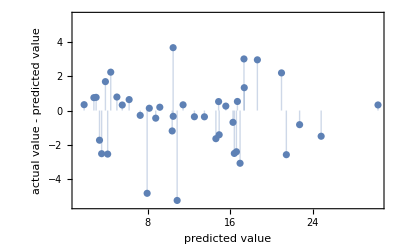

```mathematica
pmNNnoReg200["ResidualPlot"]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

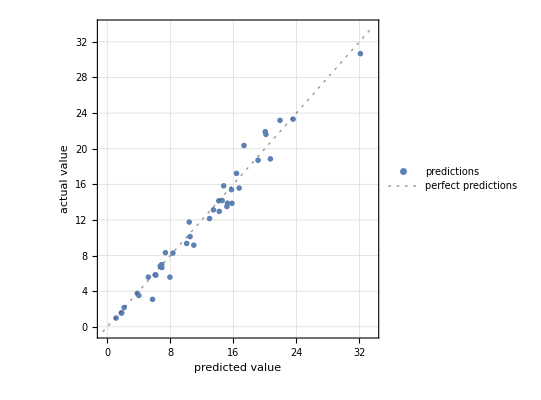

1.41434

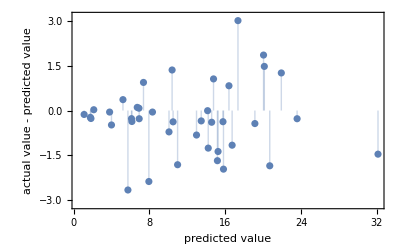

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 2.88 ± 1.4
Method | NeuralNetwork
Single evaluation time | 2.19 ms/example
Batch evaluation speed | 53.1 examples/ms
Loss | 2.49 ± 0.69
Model memory | 234. kB
Training examples used | 128 examples
Training time | 2 6
 |

```mathematica
pNN2layer200= Predict[finalTrain200,Method->{"NeuralNetwork", "NetworkDepth"->2,"NetworkType"->"FullyConnected","L2Regularization"->0.05, MaxTrainingRounds->24000}]
pmNN2layer200=PredictorMeasurements[pNN2layer200,finaltest200]
pmNN2layer200["ComparisonPlot"]
pmNN2layer200["MeanSquare"]
pmNN2layer200["ResidualPlot"]
Information[pNN2layer200]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

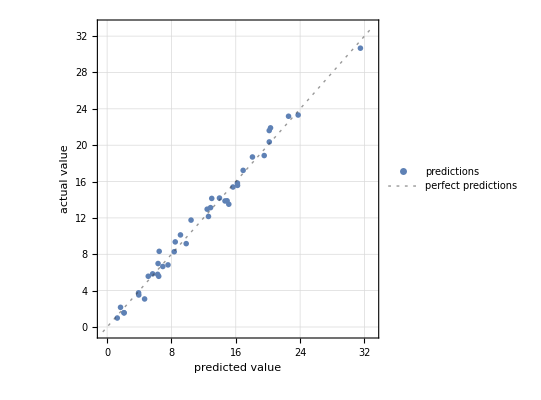

0.673797

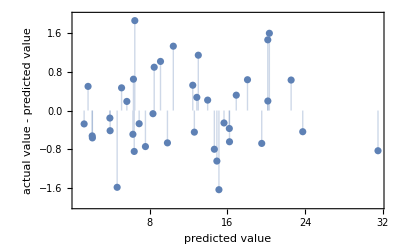

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 2.72 ± 1.5
Method | NeuralNetwork
Single evaluation time | 3.3 ms/example
Batch evaluation speed | 38.7 examples/ms
Loss | 1.94 ± 0.42
Model memory | 269. kB
Training examples used | 128 examples
Training time | 2 26
 |

```mathematica
pNN4layer200= Predict[finalTrain200,Method->{"NeuralNetwork", "NetworkDepth"->4,"NetworkType"->"FullyConnected","L2Regularization"->0.05, MaxTrainingRounds->24000}]
pmNN4layer200=PredictorMeasurements[pNN4layer200,finaltest200]
pmNN4layer200["ComparisonPlot"]
pmNN4layer200["MeanSquare"]
pmNN4layer200["ResidualPlot"]
PredictorInformation[pNN4layer200]
```

NetChain[<>]

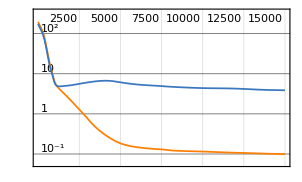
NetTrain Results
summary | ,,  batches:30000  rounds:15000  time:32s  examples/s:61616
data | ,,  training examples:128  validation examples:40  processed examples:1920000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:9.97×10^-2
validation | ,,  loss:3.88
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple200=NetChain[{BatchNormalizationLayer[],Tanh,50,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple200=NetTrain[netSimple200,finalTrain200,All,ValidationSet->finaltest200,MaxTrainingRounds->15000,Method->{"ADAM","LearningRate"->0.0003,"L2Regularization"->0.03}]
```

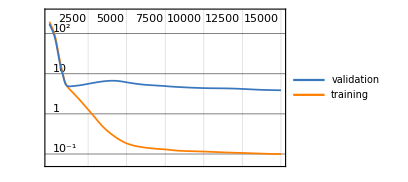
<|Loss→ | rounds
loss | -Graphics-|>

31.1608

<|Loss→0.0997103|>

14994

3.87713

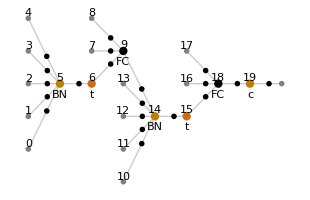

-Graphics-

```mathematica
trainedNetSimple200["FinalPlots"]
trainedNetSimple200["TotalTrainingTime"]
trainedNetSimple200["RoundMeasurements"]
best=trainedNetSimple200["BestValidationRound"]
trainedNetSimple200["ValidationLossList"][[best]]
NetInformation[trainedNetSimple200["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple200["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

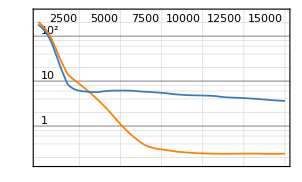
NetTrain Results
summary | ,,  batches:30000  rounds:15000  time:32s  examples/s:61441
data | ,,  training examples:128  validation examples:40  processed examples:1920000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.43×10^-1
validation | ,,  loss:3.61
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple200v2=NetChain[{BatchNormalizationLayer[],Tanh,25,BatchNormalizationLayer[],Tanh,1},"Input"->10,"Output"->"Scalar"]
trainedNetSimple200v2=NetTrain[netSimple200v2,finalTrain200,All,ValidationSet->finaltest200,MaxTrainingRounds->15000,Method->{"ADAM","LearningRate"->0.0002,"L2Regularization"->0.05}]
```

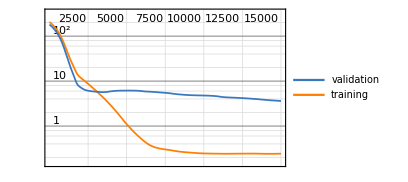
<|Loss→ | rounds
loss | -Graphics-|>

31.2493

<|Loss→0.242993|>

14986

3.61068

-Graphics-

-Graphics-

```mathematica
trainedNetSimple200v2["FinalPlots"]
trainedNetSimple200v2["TotalTrainingTime"]
trainedNetSimple200v2["RoundMeasurements"]
best=trainedNetSimple200v2["BestValidationRound"]
trainedNetSimple200v2["ValidationLossList"][[best]]
NetInformation[trainedNetSimple200v2["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple200v2["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

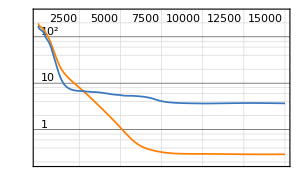
NetTrain Results
summary | ,,  batches:30000  rounds:15000  time:40s  examples/s:48103
data | ,,  training examples:128  validation examples:40  processed examples:1920000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.93×10^-1
validation | ,,  loss:3.68
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple200v3=NetChain[{BatchNormalizationLayer[],Tanh,25,25,25,25,25,BatchNormalizationLayer[],Tanh,1},"Input"->10,"Output"->"Scalar"]
trainedNetSimple200v3=NetTrain[netSimple200v3,finalTrain200,All,ValidationSet->finaltest200,MaxTrainingRounds->15000,Method->{"ADAM","LearningRate"->0.0002,"L2Regularization"->0.05}]
```

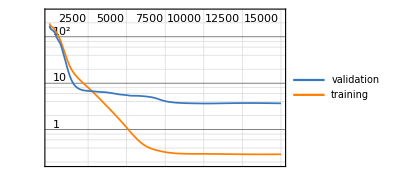
<|Loss→ | rounds
loss | -Graphics-|>

39.914

<|Loss→0.292506|>

10262

3.64528

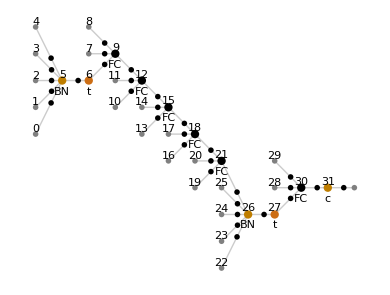

-Graphics-

```mathematica
trainedNetSimple200v3["FinalPlots"]
trainedNetSimple200v3["TotalTrainingTime"]
trainedNetSimple200v3["RoundMeasurements"]
best=trainedNetSimple200v3["BestValidationRound"]
trainedNetSimple200v3["ValidationLossList"][[best]]
NetInformation[trainedNetSimple200v3["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple200v3["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

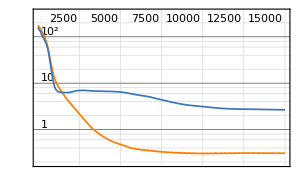
NetTrain Results
summary | ,,  batches:30000  rounds:15000  time:36s  examples/s:53878
data | ,,  training examples:128  validation examples:40  processed examples:1920000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:3.08×10^-1
validation | ,,  loss:2.65
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple200v4=NetChain[{BatchNormalizationLayer[],Tanh,50,50,50,50,50,BatchNormalizationLayer[],Tanh,1},"Input"->10,"Output"->"Scalar"]
trainedNetSimple200v4=NetTrain[netSimple200v4,finalTrain200,All,ValidationSet->finaltest200,MaxTrainingRounds->15000,Method->{"ADAM","LearningRate"->0.0002,"L2Regularization"->0.05}]
```

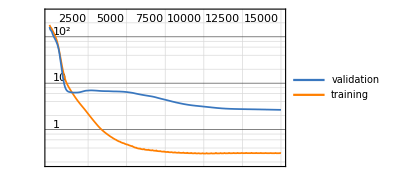
<|Loss→ | rounds
loss | -Graphics-|>

35.6362

<|Loss→0.308341|>

14964

2.61222

-Graphics-

-Graphics-

```mathematica
trainedNetSimple200v4["FinalPlots"]
trainedNetSimple200v4["TotalTrainingTime"]
trainedNetSimple200v4["RoundMeasurements"]
best=trainedNetSimple200v4["BestValidationRound"]
trainedNetSimple200v4["ValidationLossList"][[best]]
NetInformation[trainedNetSimple200v4["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple200v4["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

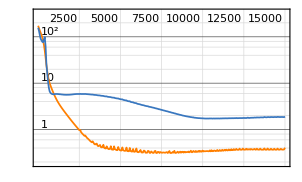
NetTrain Results
summary | ,,  batches:30000  rounds:15000  time:39s  examples/s:49944
data | ,,  training examples:128  validation examples:40  processed examples:1920000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:3.72×10^-1
validation | ,,  loss:1.87
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple200v5=NetChain[{BatchNormalizationLayer[],Tanh,50,50,50,50,50,50,50,BatchNormalizationLayer[],Tanh,1},"Input"->10,"Output"->"Scalar"]
trainedNetSimple200v5=NetTrain[netSimple200v5,finalTrain200,All,ValidationSet->finaltest200,MaxTrainingRounds->15000,Method->{"ADAM","LearningRate"->0.0003,"L2Regularization"->0.05}]
```

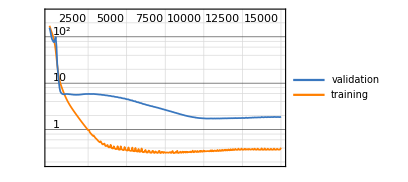
<|Loss→ | rounds
loss | -Graphics-|>

38.443

<|Loss→0.371582|>

10879

1.58206

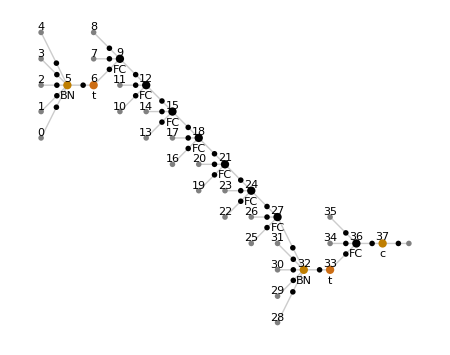

-Graphics-

```mathematica
trainedNetSimple200v5["FinalPlots"]
trainedNetSimple200v5["TotalTrainingTime"]
trainedNetSimple200v5["RoundMeasurements"]
best=trainedNetSimple200v5["BestValidationRound"]
trainedNetSimple200v5["ValidationLossList"][[best]]
NetInformation[trainedNetSimple200v5["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple200v5["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

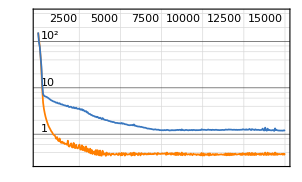
NetTrain Results
summary | ,,  batches:30000  rounds:15000  time:49s  examples/s:39868
data | ,,  training examples:128  validation examples:40  processed examples:1920000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:4.05×10^-1
validation | ,,  loss:1.6
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple200v6=NetChain[{BatchNormalizationLayer[],Tanh,100,100,100,100,100,100,100,BatchNormalizationLayer[],Tanh,1},"Input"->10,"Output"->"Scalar"]
trainedNetSimple200v6=NetTrain[netSimple200v6,finalTrain200,All,ValidationSet->finaltest200,MaxTrainingRounds->15000,Method->{"ADAM","LearningRate"->0.0005,"L2Regularization"->0.05}]
```

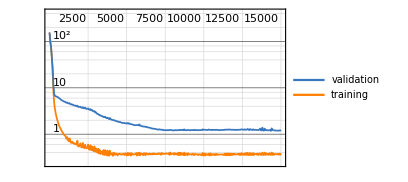
<|Loss→ | rounds
loss | -Graphics-|>

48.1588

<|Loss→0.40492|>

14395

0.964567

-Graphics-

-Graphics-

```mathematica
trainedNetSimple200v6["FinalPlots"]
trainedNetSimple200v6["TotalTrainingTime"]
trainedNetSimple200v6["RoundMeasurements"]
best=trainedNetSimple200v6["BestValidationRound"]
trainedNetSimple200v6["ValidationLossList"][[best]]
NetInformation[trainedNetSimple200v6["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple200v6["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

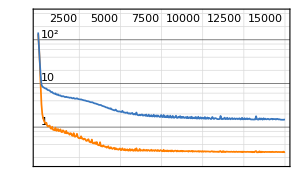
NetTrain Results
summary | ,,  batches:30000  rounds:15000  time:1.1min  examples/s:27922
data | ,,  training examples:128  validation examples:40  processed examples:1920000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.77×10^-1
validation | ,,  loss:1.46
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple200v7=NetChain[{BatchNormalizationLayer[],Tanh,250,250,250,BatchNormalizationLayer[],Tanh,1},"Input"->10,"Output"->"Scalar"]
trainedNetSimple200v7=NetTrain[netSimple200v7,finalTrain200,All,ValidationSet->finaltest200,MaxTrainingRounds->15000,Method->{"ADAM","LearningRate"->0.0005,"L2Regularization"->0.05}]
```

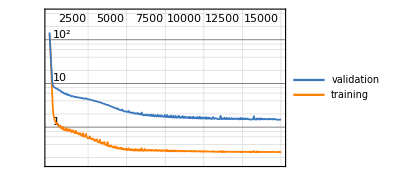
<|Loss→ | rounds
loss | -Graphics-|>

68.7619

<|Loss→0.276535|>

13193

1.33129

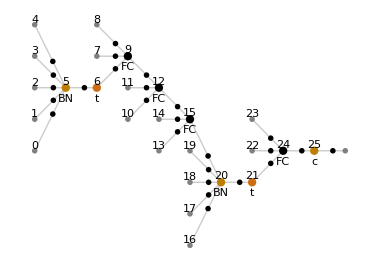

-Graphics-

```mathematica
trainedNetSimple200v7["FinalPlots"]
trainedNetSimple200v7["TotalTrainingTime"]
trainedNetSimple200v7["RoundMeasurements"]
best=trainedNetSimple200v7["BestValidationRound"]
trainedNetSimple200v7["ValidationLossList"][[best]]
NetInformation[trainedNetSimple200v7["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple200v7["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

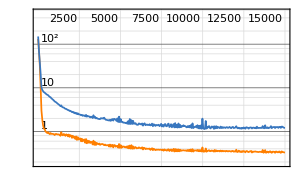
NetTrain Results
summary | ,,  batches:30000  rounds:15000  time:1.8min  examples/s:17692
data | ,,  training examples:128  validation examples:40  processed examples:1920000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:3.26×10^-1
validation | ,,  loss:1.2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple200v8=NetChain[{BatchNormalizationLayer[],Tanh,250,250,250,250,250,BatchNormalizationLayer[],Tanh,1},"Input"->10,"Output"->"Scalar"]
trainedNetSimple200v8=NetTrain[netSimple200v8,finalTrain200,All,ValidationSet->finaltest200,MaxTrainingRounds->15000,Method->{"ADAM","LearningRate"->0.0005,"L2Regularization"->0.05}]
```

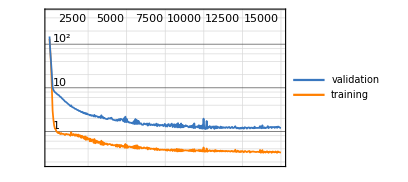
<|Loss→ | rounds
loss | -Graphics-|>

108.521

<|Loss→0.326359|>

9900

1.02354

-Graphics-

-Graphics-

```mathematica
trainedNetSimple200v8["FinalPlots"]
trainedNetSimple200v8["TotalTrainingTime"]
trainedNetSimple200v8["RoundMeasurements"]
best=trainedNetSimple200v8["BestValidationRound"]
trainedNetSimple200v8["ValidationLossList"][[best]]
NetInformation[trainedNetSimple200v8["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple200v8["TrainedNet"],"SummaryGraphic"]
```

```mathematica
netSimple200v9=NetChain[{BatchNormalizationLayer[],Tanh,100,100,100,100,100,100,100,BatchNormalizationLayer[],Tanh,1},"Input"->10,"Output"->"Scalar"]
trainedNetSimple200v9=NetTrain[netSimple200v9,finalTrain200,All,ValidationSet->finaltest200,MaxTrainingRounds->15000,Method->{"ADAM","LearningRate"->0.0005,"L2Regularization"->0.05}]
```

NetChain[<>]

NetTrain Results
summary | ,,  batches:30000  rounds:15000  time:48s  examples/s:40418
data | ,,  training examples:128  validation examples:40  processed examples:1920000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:4.05×10^-1
validation | ,,  loss:1.6
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
trainedNetSimple200v9["FinalPlots"]
trainedNetSimple200v9["TotalTrainingTime"]
trainedNetSimple200v9["RoundMeasurements"]
best=trainedNetSimple200v9["BestValidationRound"]
trainedNetSimple200v9["ValidationLossList"][[best]]
NetInformation[trainedNetSimple200v9["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple200v9["TrainedNet"],"SummaryGraphic"]
```

<|Loss→ | rounds
loss | -Graphics-|>

47.5036

<|Loss→0.40492|>

14395

0.964567

-Graphics-

-Graphics-